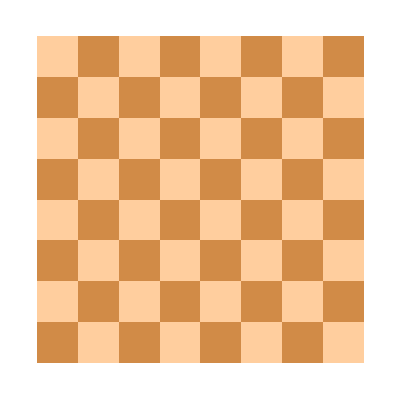

```mathematica
dark=RGBColor[0.8196,0.5451,0.2784];
light=RGBColor[1,0.8078,0.6196];
queen=-Graphics-;
range=Partition[Range[64],8];
range=MapAt[Boole[EvenQ[#]]&,range,1;;8;;2];
range=MapAt[Boole[OddQ[#]]&,range,2;;8;;2];

board=Array[List,{8,8}];

drawBoard[board_]:=ArrayPlot[range,ColorRules->{0->light,1->dark},Epilog->(Inset[queen,#-1,#-1,1]&/@Position[board,1])]
(*ListAnimate[drawBoard/@{{{0,1,0,0,0,0,0,0}}}]*)
drawBoard[{{0,1,0,0,0,0,0,0}}]
```

```mathematica
Import["http://upload.wikimedia.org/wikipedia/commons/thumb/1/15/Chess_qlt45.svg/200px-Chess_qlt45.svg.png"]
```

-Graphics-

```mathematica
-Graphics-//Print;
```

-Graphics-

```mathematica
({{♜, ♞, ♝, ♛, ♚, ♝, ♞, ♜}, {♟, ♟, ♟, ♟, ♟, ♟, ♟, ♟}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {♙, ♙, ♙, ♙, ♙, ♙, ♙, ♙}, {♖, ♘, ♗, ♕, ♔, ♗, ♘, ♖}});
```

```mathematica
({{"♜", "♞", "♝", "♛", "♚", "♝", "♞", "♜"}, {"♟", "♟", "♟", "♟", "♟", "♟", "♟", "♟"}, {"□", "□", "□", "□", "□", "□", "□", "□"}, {"□", "□", "□", "□", "□", "□", "□", "□"}, {"□", "□", "□", "□", "□", "□", "□", "□"}, {"□", "□", "□", "□", "□", "□", "□", "□"}, {"♙", "♙", "♙", "♙", "♙", "♙", "♙", "♙"}, {"♖", "♘", "♗", "♕", "♔", "♗", "♘", "♖"}});
```

```mathematica
"1. g3 g6 2. b3 b6 3. e3 e6 4. d3 d6 5. Ke2 Kd7 6. Kf3 Kc6 7. Qe2 Qd7 8. Kg4 Kb5 9. Qf3 Qc6 10. Kg5 Kb4 11. Nh3 Nh6 12. Na3 Na6 13. Nf4 Nf5 14. Nc4 Nc5 15. Kf6 Kc3 16. Bh3 Bh6 17. Ba3 Ba6 18. Nh5 Nh4 19. Na5 Na4 20. Ke7 Kd2 21. Qf6 Qc3 22. Kd7 Ke2 23. Qe7 Qd2 24. Nf6 Nf3 25. Nc6 Nc3 26. Ng8 Ng1 27. Nb8 Nb1 28. Qd8 Qd1 29. Ke8 Ke1 30. e4 e5 31. d4 d5 32. Bc8 Bc1 33. Bf8 Bf1 34. g4 g5 35. b4 b5 36. h4 h5 37. a4 a5 38. Rh3 Rh6 39. Raa3 Raa6 40. Rhc3 Raf6 41. Rc6 Rf3 42. Ra6 Rh3 43. Rf3 Rc6 44. Rf6 Rcc3 45. Rh6 Ra3 46. Rh8 Rh1 47. Ra8 Ra1 48. f4 f5 49. c4 c5*"
```

1. g3 g6 2. b3 b6 3. e3 e6 4. d3 d6 5. Ke2 Kd7 6. Kf3 Kc6 7. Qe2 Qd7 8. Kg4 Kb5 9. Qf3 Qc6 10. Kg5 Kb4 11. Nh3 Nh6 12. Na3 Na6 13. Nf4 Nf5 14. Nc4 Nc5 15. Kf6 Kc3 16. Bh3 Bh6 17. Ba3 Ba6 18. Nh5 Nh4 19. Na5 Na4 20. Ke7 Kd2 21. Qf6 Qc3 22. Kd7 Ke2 23. Qe7 Qd2 24. Nf6 Nf3 25. Nc6 Nc3 26. Ng8 Ng1 27. Nb8 Nb1 28. Qd8 Qd1 29. Ke8 Ke1 30. e4 e5 31. d4 d5 32. Bc8 Bc1 33. Bf8 Bf1 34. g4 g5 35. b4 b5 36. h4 h5 37. a4 a5 38. Rh3 Rh6 39. Raa3 Raa6 40. Rhc3 Raf6 41. Rc6 Rf3 42. Ra6 Rh3 43. Rf3 Rc6 44. Rf6 Rcc3 45. Rh6 Ra3 46. Rh8 Rh1 47. Ra8 Ra1 48. f4 f5 49. c4 c5*